```mathematica
$Assumptions=x>0&&x≠1
Old=Q(1/12+(1-5x-2x^2)/(8(1-x)^3)-3x^2Log[x]/(4(1-x)^4))+1/8+(3-9x)/(8(1-x)^2)-3x^2 Log[x]/(4(1-x)^3)
```

x>0&&x≠1

1/8+(3-9 x)/(8 (1-x)^2)-(3 x^2 Log[x])/(4 (1-x)^3)+Q (1/12+(1-5 x-2 x^2)/(8 (1-x)^3)-(3 x^2 Log[x])/(4 (1-x)^4))

```mathematica
2(1-x)^4(Old)/.Q->-1//Simplify
```

1/12 (7-31 x+60 x^2-37 x^3+x^4+18 x^3 Log[x])

```mathematica
Old2=1/8Integrate[(Q y+1)y(1-y)/(1-(1-x)y)*(1-(2+x)y(1-y)/(3(1-(1-x)y))),{y,0,1}]
```

-1/(288 (-1+x)^6)(-(-1+x) (2 (-1+x) (5+x (-51+x (-33+7 x)))+Q (-6+x (91+x (123+x (-33+5 x)))))+12 x (1+Q+11 x+14 Q x+(-13+x) x^2) Log[x])

```mathematica
m[1]/MWR//N
m[2]/MWR//N
```

0.420455

4.54545

```mathematica
F[0.4]//N
F[4.5]//N
```

1.53142

1.15306

```mathematica
Plot[F[x],{x,0,10}]
```

```mathematica
Limit[F[x],x->∞]
```

2/3

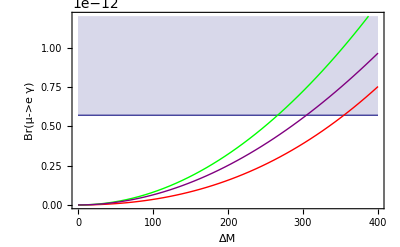

```mathematica
al=1/137;
MW=80.385`500 gev;
(*MW=60 gev;*)
mmu=105/1000 gev;
m[1]=M0 gev;
m[2]=m[1]+dM gev;
m[3]=925 gev;



(*m[1]=1*10^-45 gev;
m[2]=Sqrt[7.59`200*10^-5]*10^-9 gev;
m[3]=Sqrt[2.32`200*10^-3]*10^-9gev;*)
(*m[1]=10^-50 gev;
m[2]=Sqrt[2]gev;
m[3]=10^-50 gev;*)

MWR=2200 gev;
(*MWR=MW;*)
KR={{c13,0,s13},{0,1,0},{-Exp[I p]s13,0,Exp[I p]c13}};
KR={{1/Sqrt[2],1/Sqrt[2],0},{-1/Sqrt[2],1/Sqrt[2],0},{0,0,1}};
(*KR={{Sqrt[2/3],Sqrt[1/3],0},{-1/Sqrt[6],Sqrt[1/3],Sqrt[1/2]},{Sqrt[1/6],-1/Sqrt[3],Sqrt[1/2]}};*)
Clear[V1]
V1[i_]:=ConjugateTranspose[KR][[1,i]]KR[[i,2]];
(*V1[a_]:=1/3;*)
(*V1[1]=0
V1[2]=0
V1[3]=0*)
V4[1]=0;
V4[2]=0;
V4[3]=0;

F[r_]:=1/(6(1-r)^4)(10-43r+78r^2-49r^3+4r^4+18r^3 Log[r]);
G[r_]:=1/(1-r)^3(-4+15r-12r^2+r^3+6r^2 Log[r]);
Clear[hL,hR]
hL=0;
hR=MW^2/MWR^2Sum[V1[i]F[m[i]^2/MWR^2]+m[i]/mmu V4[i]G[m[i]^2/MWR^2],{i,1,3}];
Clear[Br];
Br=3al/(8 Pi)(Abs[hL]^2+Abs[hR]^2)//N;

Plot[{5.7 10^-13,Br/.M0->500,Br/.M0->1500,Br/.M0->2500},{dM,0,400},PlotRange->{0,12 10^-13},PlotStyle->{Thick,Directive[Red,Thick],Directive[Green,Thick],Directive[Purple,Thick]},Filling->{1->Top},Frame->True,FrameLabel->{"ΔM","Br(μ->e γ)"}]
```

```mathematica
gev=1
```

1

```mathematica
Br
```

```mathematica
M0
```

M0

FindRoot::precw: The precision of the argument function ({1.553×10^-9\ Abs[0.821382  - 0.0833333\ Power[« 2 »]\ Plus[« 6 »]]^2 == « 537 »}) is less than WorkingPrecision (160.).

FindRoot::precw: The precision of the argument function ({1.553×10^-9\ Abs[0.820935  - 0.0833333\ Power[« 2 »]\ Plus[« 6 »]]^2 == « 537 »}) is less than WorkingPrecision (160.).

FindRoot::precw: The precision of the argument function ({1.553×10^-9\ Abs[0.820482  - 0.0833333\ Power[« 2 »]\ Plus[« 6 »]]^2 == « 537 »}) is less than WorkingPrecision (160.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

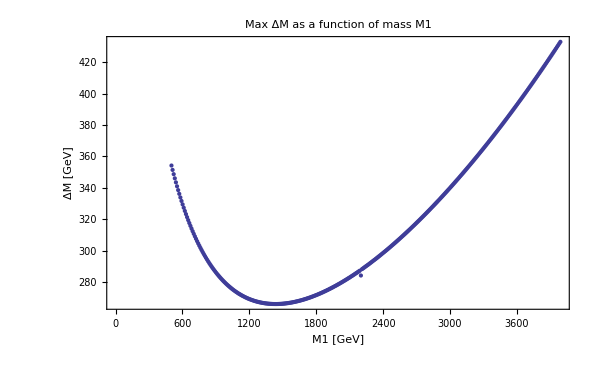

1.553×10^-9 Abs[(-3.36139×10^23+1.60932×10^22 dM-1.76403×10^19 dM^2-6.31184×10^16 dM^3-2.01996×10^13 dM^4+1.49982×10^10 dM^5+7.27717×10^6 dM^6+1952.37 dM^7+0.488093 dM^8+(-1.13438×10^23-1.36125×10^21 dM-6.80625×10^18 dM^2-1.815×10^16 dM^3-2.7225×10^13 dM^4-2.178×10^10 dM^5-7.26×10^6 dM^6) Log[2.06612×10^-7 (500.+dM)^2])/(4.59×10^6-1000. dM-1. dM^2)^4]^2

```mathematica
tab=Table[{M0,dM/.FindRoot[{Br==5.7`500*10^-13},{dM,200},MaxIterations->200,WorkingPrecision->160]},{M0,501,4000,10}];
ListPlot[tab,Frame->True,FrameLabel->{"M1 [GeV]","ΔM [GeV]"},PlotLabel->"Max ΔM as a function of mass M1"]
```

```mathematica
ep^2/.ep->(m[1]^2-m[2]^2)/(2MWR^2)//N
```

104.902

```mathematica
m[1]/MWR
m[2]/MWR
```

37/88

50/11

```mathematica
1.8607491327481232*^-10
```

1.86075×10^-10

```mathematica
KR.Transpose[KR]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
V1[i_]:=ConjugateTranspose[KR][[1,i]]KR[[i,2]];
Vx[i_]:=ConjugateTranspose[KR][[2,i]]KR[[i,1]];
```

```mathematica
V1[1]
Vx[1]
```

(√2)/3

(√2)/3

```mathematica
24/32
```

3/4

```mathematica
24 Pi^2/(Gf^2 mm^2 mm^2)F2^2/.F2->mm^2/(32 Pi^2 mW^2)g/Sqrt[2]/.Gf->Sqrt[2]/8 g^2/mW^2
```

3/(8 g^2 π^2)

```mathematica
m42/(m42-q2)//Apart
```

```mathematica
1.8607491327481232*^-10*()
```

```mathematica
V1[1]
V1[2]
```

1/2

-1/2

```mathematica
F[x]
```

(10-43 x+78 x^2-49 x^3+4 x^4+18 x^3 Log[x])/(6 (1-x)^4)

```mathematica
Fp=-x(1+2x)/(8(1-x^2)^2)+3x^2/(4(1-x)^2)(x/(1-x)^2(1-x+Log[x])+1)
```

-(x (1+2 x))/(8 (1-x^2)^2)+(3 x^2 (1+(x (1-x+Log[x]))/(1-x)^2))/(4 (1-x)^2)

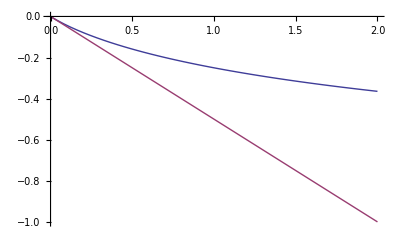

```mathematica
Plot[{(F[x]-5/3),(-x/2)},{x,0,2}]
```

```mathematica
Limit[F[x],{x->0}]
```

{5/3}

```mathematica
Limit[Fp,x->∞]
```

0

```mathematica
Series[F[x],{x,0,3}]
```

5/3-x/2+x^2+(11/2+3 Log[x]) x^3+O[x]^4

```mathematica
10^-3/(80 10^9)^2//N
```

1.5625×10^-25

```mathematica
F[x]
```

(10-43 x+78 x^2-49 x^3+4 x^4+18 x^3 Log[x])/(6 (1-x)^4)

```mathematica
F1[x_]:=1/(3(x-1)^4)(-2x^3-3x^2+6x-1+6x^2Log[x])
F3[x_]:=1/(x-1)^4(-x^3+6x^2-3x-2x-6x)
```

```mathematica
Series[F[x],{x,0,1}]
Series[F1[x],{x,0,1}]
Series[F3[x],{x,0,1}]
```

5/3-x/2+O[x]^2

-1/3+(2 x)/3+O[x]^2

-11 x+O[x]^2

```mathematica
2/3
```